(ⅇ^(-2 √(1-b^2) α) (8+8 √(1-b^2) α+α^2+8 ⅇ^(2 √(1-b^2) α) (-1+√(1-b^2) α)))/α^2

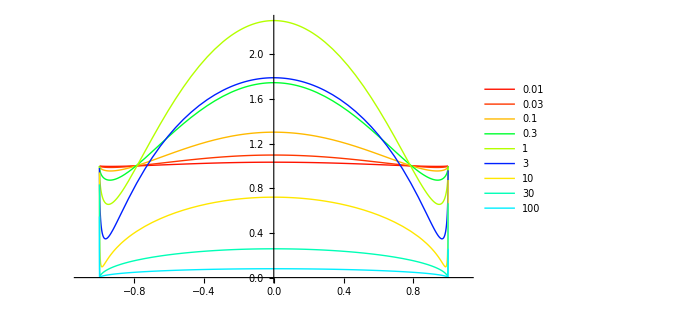

```mathematica
Remove["Global`*"]
S[τ_]=Bo (1-(τ/(R α))^2+(2 τ √(R^2-b^2))/(R^2 α)-1);
Io=1;Bo=4;R=1;
Intensity[b_,α_]=Exp[-τν](Io+ Integrate[S[τ]Exp[τ],{τ,0,τν}]   )/.τν->2α √(R^2-b^2) //FullSimplify
αo={.01,.03,.1,.3,1,3,10,30,100};
limbs=Intensity[b,αo];
Plot[limbs,{b,-R(1.1),R(1.1)},PlotStyle->Table[{Thick,Hue[(αo[[i]]/Norm[αo])*255/2]},{i,1,9}],PlotLegends->αo,ImageSize->500]
```